1024

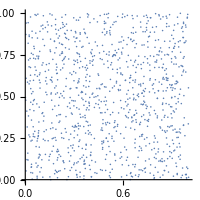
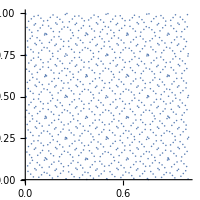

qmc.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
R=2^10

Rands=BlockRandom[SeedRandom[1];
RandomReal[1,{R,2}]];
Sobols=BlockRandom[SeedRandom[1,Method->{"MKL",Method->{"Sobol","Dimension"->2}}];
RandomReal[1,{R,2}]];

P=Row[{ListPlot[Rands,AspectRatio->1,ImageSize-> {200,200},PlotRange->{{0,1},{0,1}}],
ListPlot[Sobols,AspectRatio->1,ImageSize-> {200,200},PlotRange->{{0,1},{0,1}}]}, "        "]
Export["qmc.pdf",P]
```